```mathematica
{{}{}{}{}{}}
```

```mathematica
a={{-6.2500*^+21,3.3333*^+21,-2.0833*^+20,0,0},
{3.3333*^+21,-6.2500*^+21,3.3333*^+21,-2.0833*^+20,0},
{-2.0833*^+20,3.3333*^+21,-6.2500*^+21,3.3333*^+21,-2.0833*^+20},
{0,-2.0833*^+20,3.3333*^+21,-6.2500*^+21,-2.0833*^+20},
{0,0,-2.0833*^+20,-2.0833*^+20,-2.0833*^+20}};

b=Eigenvalues[A]
b=DiagonalMatrix[b]
c=Eigenvectors[A]
c.b.Inverse[c]
```

{-1.1831×10^22,-8.12531×10^21,-4.01336×10^21,-1.08742×10^21,-1.51228×10^20}

{{-1.1831×10^22,0.,0.,0.,0.},{0.,-8.12531×10^21,0.,0.,0.},{0.,0.,-4.01336×10^21,0.,0.},{0.,0.,0.,-1.08742×10^21,0.},{0.,0.,0.,0.,-1.51228×10^20}}

{{-0.378876,0.597043,-0.597093,0.378758,-0.00391352},{0.606175,-0.363758,-0.363613,0.606611,0.00639434},{0.595366,0.375702,-0.380596,-0.597217,-0.0535364},{-0.362672,-0.598298,-0.585529,-0.345013,-0.220524},{-0.0548966,-0.110036,-0.15352,-0.113415,0.973882}}

{{-6.1815×10^21,3.36064×10^21,1.80035×10^20,1.55987×10^19,-3.28688×10^19},{3.36064×10^21,-6.3532×10^21,-3.32073×10^21,2.05934×10^20,-8.16907×10^19},{1.80035×10^20,-3.32073×10^21,-6.31016×10^21,3.26078×10^21,4.2232×10^20},{1.55987×10^19,2.05934×10^20,3.26078×10^21,-5.97743×10^21,-1.14131×10^21},{-3.28688×10^19,-8.16907×10^19,4.2232×10^20,-1.14131×10^21,-3.86044×10^20}}

```mathematica
A={{3.0,2.0,2.0},{4.0,5.0,3.0},{6.0,4.0,8.0}}

b=Eigenvalues[A]
b=DiagonalMatrix[b]
c=Eigenvectors[A]
c.b.Inverse[c]
```

{{3.,2.,2.},{4.,5.,3.},{6.,4.,8.}}

{12.3886,2.80586,0.805507}

{{12.3886,0.,0.},{0.,2.80586,0.},{0.,0.,0.805507}}

{{-0.280012,-0.487402,-0.827063},{-0.150304,-0.691741,0.706331},{-0.789115,0.467896,0.397958}}

{{3.46333,1.48735,2.88378},{1.89108,2.31708,1.2473},{5.50177,1.13812,10.2196}}

```mathematica
hbar=1.0545718*^-34;
k=572.9365924;
u=1.660539040*^-27;
m=1.00794*u;
ω=Sqrt[k/m];

ni=1;
en=hbar ω(ni+1/2)
xi=10*^-12;

1/Sqrt[2^ni ni!](m ω/(Pi hbar))^(1/4)Exp[-m ω xi^2/(2hbar)]HermiteH[ni,Sqrt[m ω/hbar]xi]
```

9.25505×10^-20

103637. HermiteH[n,0.963628]

```mathematica
ni=50;
Plot[1/Sqrt[2^ni ni!](m ω/(Pi hbar))^(1/4)Exp[-m ω x^2/(2hbar)]HermiteH[ni,Sqrt[m ω/hbar]x],{x,-50*^-12,50*^-12}]
ψ[n_,x_]:=1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-x^2/2] HermiteH[n,x]
N@ψ[1,10*^-12]
```

-Graphics-

1.06225×10^-11

```mathematica
eigvallist
```

{3.08501×10^-20,9.25501×10^-20,1.54249×10^-19,2.15948×10^-19,2.77647×10^-19,3.39357×10^-19,4.01131×10^-19,4.63157×10^-19,5.25942×10^-19,5.90474×10^-19,6.58168×10^-19,7.30489×10^-19,8.08559×10^-19,8.93012×10^-19,9.84108×10^-19,1.08191×10^-18,1.18637×10^-18,1.29746×10^-18,1.41509×10^-18,1.53921×10^-18,1.66976×10^-18,1.80668×10^-18,1.94992×10^-18,2.09941×10^-18,2.2551×10^-18,2.41692×10^-18,2.58481×10^-18,2.7587×10^-18,2.9385×10^-18,3.12414×10^-18,3.31553×10^-18,3.51258×10^-18,3.71517×10^-18,3.92321×10^-18,4.13657×10^-18,4.35513×10^-18,4.57875×10^-18,4.8073×10^-18,5.04062×10^-18,5.27855×10^-18,5.52092×10^-18,5.76755×10^-18,6.01827×10^-18,6.27286×10^-18,6.53114×10^-18,6.79287×10^-18,7.05784×10^-18,7.32581×10^-18,7.59655×10^-18,7.8698×10^-18,8.14531×10^-18,8.4228×10^-18,8.70201×10^-18,8.98264×10^-18,9.26441×10^-18,9.54703×10^-18,9.83018×10^-18,1.01136×10^-17,1.03968×10^-17,1.06797×10^-17,1.09618×10^-17,1.12429×10^-17,1.15226×10^-17,1.18005×10^-17,1.20763×10^-17,1.23497×10^-17,1.26203×10^-17,1.28878×10^-17,1.31518×10^-17,1.34121×10^-17,1.36681×10^-17,1.39197×10^-17,1.41664×10^-17,1.44079×10^-17,1.4644×10^-17,1.48741×10^-17,1.50981×10^-17,1.53156×10^-17,1.55263×10^-17,1.57299×10^-17,1.5926×10^-17,1.61144×10^-17,1.62948×10^-17,1.64669×10^-17,1.66304×10^-17,1.6785×10^-17,1.69305×10^-17,1.70665×10^-17,1.71928×10^-17,1.7309×10^-17,1.74147×10^-17,1.75093×10^-17,1.75922×10^-17,1.76594×10^-17,1.77249×10^-17,1.77437×10^-17,1.78612×10^-17,1.78793×10^-17,1.80801×10^-17,1.81034×10^-17}

```mathematica
eigvallist
```

{3.08493×10^-20,9.25443×10^-20,1.54229×10^-19,2.15897×10^-19,2.77542×10^-19,3.39169×10^-19,4.00816×10^-19,4.62641×10^-19,5.25073×10^-19,5.88964×10^-19,6.55561×10^-19,7.26218×10^-19,8.02023×10^-19,8.83598×10^-19,9.7115×10^-19,1.06463×10^-18,1.16384×10^-18,1.26855×10^-18,1.37845×10^-18,1.49324×10^-18,1.61256×10^-18,1.73604×10^-18,1.86327×10^-18,1.99382×10^-18,2.1272×10^-18,2.26293×10^-18,2.40047×10^-18,2.53926×10^-18,2.67871×10^-18,2.8182×10^-18,2.95709×10^-18,3.09473×10^-18,3.23045×10^-18,3.36355×10^-18,3.49333×10^-18,3.61908×10^-18,3.7401×10^-18,3.85563×10^-18,3.96495×10^-18,4.06727×10^-18,4.16176×10^-18,4.24742×10^-18,4.32319×10^-18,4.38386×10^-18,4.44321×10^-18,4.46953×10^-18,4.57642×10^-18,4.61374×10^-18,4.79362×10^-18,4.84113×10^-18}

```mathematica
eigvallist=ReadList["~/phd-stuff/courses/comp_phys/eigenvalues",Real,RecordLists->True];
eigvallist=Flatten@eigvallist;
eigvallist[[1]]
```

3.08501×10^-20

1000

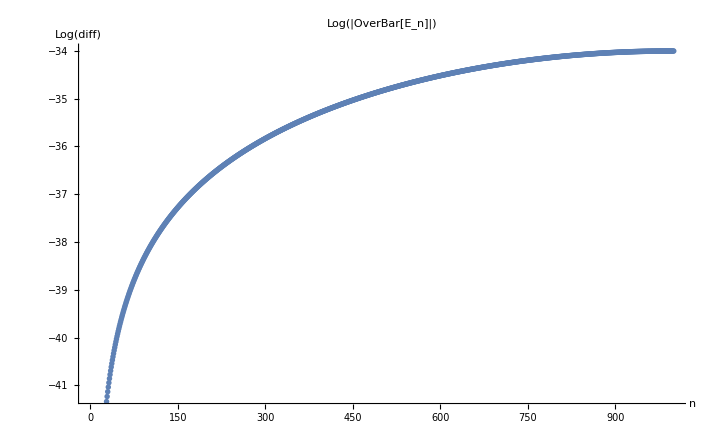

```mathematica
eigvallist=ReadList["~/phd-stuff/courses/comp_phys/eigenvalues",Real,RecordLists->True];
eigvallist=Flatten@eigvallist;

Length[%]

hbar=1.0545718*^-34;
k=572.9365924;
u=1.660539040*^-27;
m=1.00794*u;
ω=Sqrt[k/m];

aneigvallist=Table[hbar ω(n+1/2),{n,0,Length[eigvallist]-1}];

eigvalcomp=Log[Abs[aneigvallist-eigvallist]];

ListPlot[eigvalcomp,PlotLabel->"Log(|OverBar[E_n]|)",AxesLabel->{"n","Log(diff)"}]
```

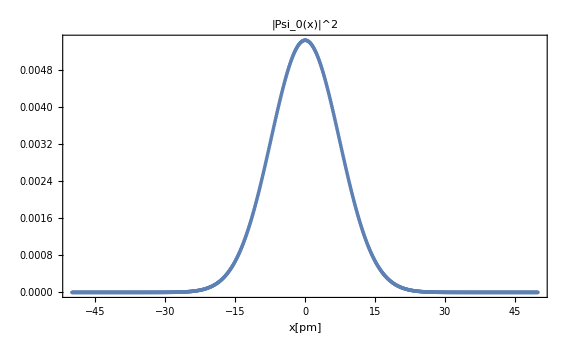

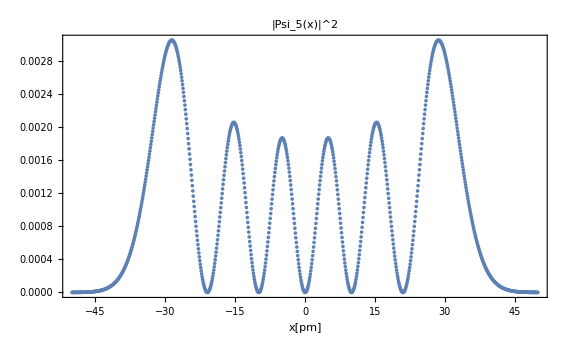

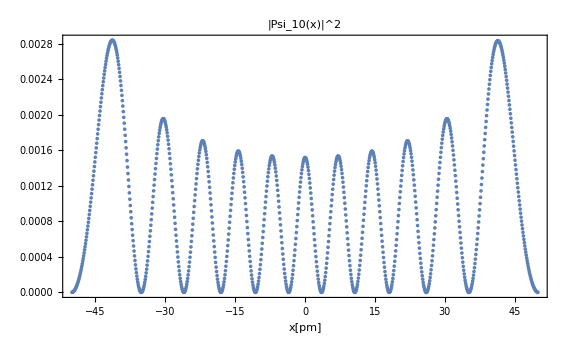

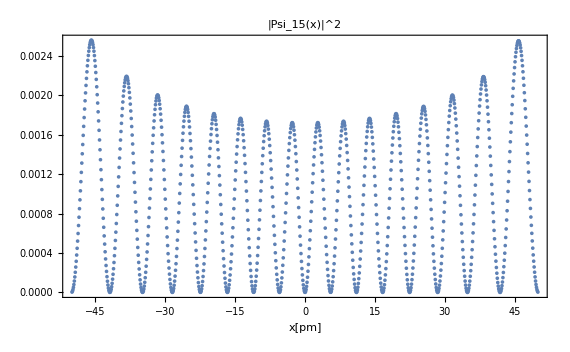

```mathematica
list=ReadList["~/phd-stuff/courses/comp_phys/eigenvectors",Real,RecordLists->True];
list=Transpose[list]^2;
ListPlot[list[[1]],PlotLabel->"|Psi_0(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[6]],PlotLabel->"|Psi_5(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[11]],PlotLabel->"|Psi_10(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[16]],PlotLabel->"|Psi_15(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
```

```mathematica
ψ[n_,x_]:=1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-x^2/2] HermiteH[n,x];
Manipulate[
Plot[Evaluate[ψ[n,x]^2],Evaluate@{x,-Sqrt[n]-2.5,Sqrt[n]+2.5},Frame->True,Axes->False,PlotPoints->100,PlotLabel->StringForm["|Psi_``(x)|^2",n]],
{{n,0,"energy level"},0,30,1},SaveDefinitions->True]
```

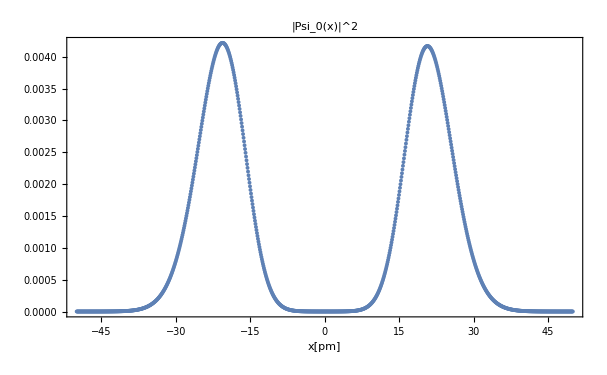

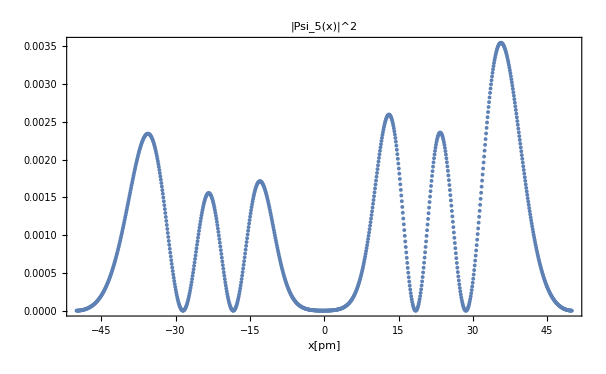

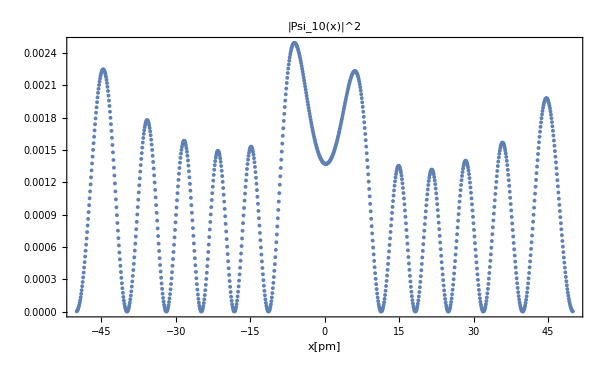

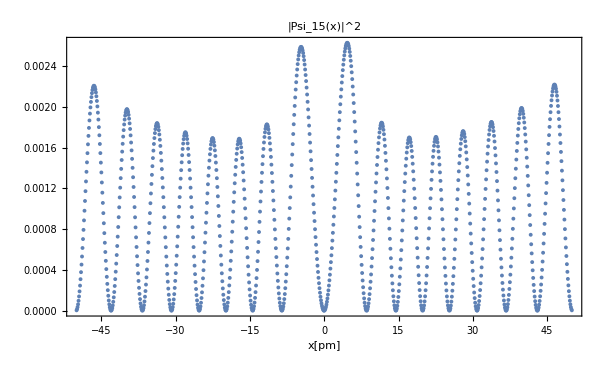

```mathematica
list=ReadList["~/phd-stuff/courses/comp_phys/eigenvectors2",Real,RecordLists->True];
list=Transpose[list]^2;
ListPlot[list[[1]],PlotLabel->"|Psi_0(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[6]],PlotLabel->"|Psi_5(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[11]],PlotLabel->"|Psi_10(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
ListPlot[list[[16]],PlotLabel->"|Psi_15(x)|^2",AxesLabel->{"x[pm]",""},DataRange->{-50,50},Frame->True,Axes->False]
```